```mathematica
f[i_,n_]:=PDF[NormalDistribution[Subscript[x,i],1/√n],Subscript[x,i+1]](1-Exp[-2 n (Subscript[g,i+1] - Subscript[x,i+1])(Subscript[g,i] - Subscript[x,i])])
```

```mathematica
f[i_,n_]:=PDF[NormalDistribution[Subscript[x,i],1/√n],Subscript[x,i+1]](1-Exp[-2 n (g - Subscript[x,i+1])(g - Subscript[x,i])])
```

```mathematica
i[n_]:=∏_(i=0)^(n-1) f[i,n]
```

```mathematica
i[1]/.g-> 3
```

(ⅇ^(-1/2 (-x_0+x_1)^2) (1-ⅇ^(-2 (3-x_0) (3-x_1))))/(√(2 π))

```mathematica
Plot3D[i[1]/.g-> 3,{Subscript[x, 0],-3,3},{Subscript[x, 1],-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[D[i[1],{Subscript[x, 1],1}]/.g-> 3],{Subscript[x, 0],-7,7},{Subscript[x, 1],-7,7},PlotRange->Full]
```

-Graphics3D-

```mathematica
D[i[3],{Subscript[x, 1],2}]/. g-> 3
```

-1/π^(3/2)27 √6 ⅇ^(-3/2 (-x_0+x_1)^2-6 (3-x_1) (3-x_2)-3/2 (-x_1+x_2)^2-3/2 (-x_2+x_3)^2) (1-ⅇ^(-6 (3-x_0) (3-x_1))) (1-ⅇ^(-6 (3-x_2) (3-x_3))) (3-x_2)^2-1/π^(3/2)12 ⅇ^(-6 (3-x_1) (3-x_2)) (1-ⅇ^(-6 (3-x_2) (3-x_3))) (3-x_2) (-9 √(3/2) ⅇ^(-6 (3-x_0) (3-x_1)-3/2 (-x_0+x_1)^2-3/2 (-x_1+x_2)^2-3/2 (-x_2+x_3)^2) (3-x_0)+3/2 √(3/2) ⅇ^(-3/2 (-x_0+x_1)^2-3/2 (-x_1+x_2)^2-3/2 (-x_2+x_3)^2) (1-ⅇ^(-6 (3-x_0) (3-x_1))) (-3 (-x_0+x_1)+3 (-x_1+x_2)))+1/(2 π^(3/2))3 √(3/2) (1-ⅇ^(-6 (3-x_1) (3-x_2))) (1-ⅇ^(-6 (3-x_2) (3-x_3))) (-36 ⅇ^(-6 (3-x_0) (3-x_1)-3/2 (-x_0+x_1)^2-3/2 (-x_1+x_2)^2-3/2 (-x_2+x_3)^2) (3-x_0)^2-12 ⅇ^(-6 (3-x_0) (3-x_1)-3/2 (-x_0+x_1)^2-3/2 (-x_1+x_2)^2-3/2 (-x_2+x_3)^2) (3-x_0) (-3 (-x_0+x_1)+3 (-x_1+x_2))+(1-ⅇ^(-6 (3-x_0) (3-x_1))) (-6 ⅇ^(-3/2 (-x_0+x_1)^2-3/2 (-x_1+x_2)^2-3/2 (-x_2+x_3)^2)+ⅇ^(-3/2 (-x_0+x_1)^2-3/2 (-x_1+x_2)^2-3/2 (-x_2+x_3)^2) (-3 (-x_0+x_1)+3 (-x_1+x_2))^2))

```mathematica
D[∏_(i=0)^2 f[i],{Subscript[x, 1],1}]
```

1/(2 √2 π^(3/2))ⅇ^(-2 n (g_0-x_0) (g_1-x_1)-1/2 n (-x_0+x_1)^2-2 n (g_1-x_1) (g_2-x_2)-1/2 n (-x_1+x_2)^2-2 n (g_2-x_2) (g_3-x_3)-1/2 n (-x_2+x_3)^2) n^(3/2) (2 n (g_0-x_0)-n (-x_0+x_1)+2 n (g_2-x_2)+n (-x_1+x_2))

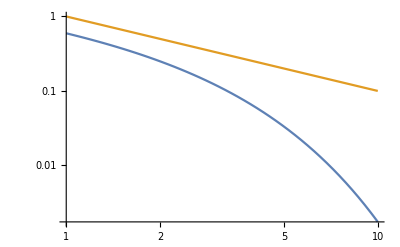

```mathematica
LogLogPlot[{1/(√n) Exp[-0.52n],1/n},{n,1,10}]
```

```mathematica
exactlimit[a_,b_]:=CDF[NormalDistribution[0,1],b + a]- Exp[-2 a b]*CDF[NormalDistribution[0,1],b-a]
```

```mathematica
exactlimit[1,1]//N
```

0.909582

```mathematica
∫_(-∞)^2 PDF[NormalDistribution[0,1],x](1-Exp[-2  (2 -x)])ⅆx//N
```

0.909582

```mathematica
s[h_]:=∑_(k=-10/h)^(2/h) PDF[NormalDistribution[0,1], k h](1-Exp[-2  (2 -k h)]) h
```

```mathematica
Block[{$MaxExtraPrecision=10000},N[s[1/82],10]]
```

0.9095808882

```mathematica
N[s[1/82]]
```

0.909581

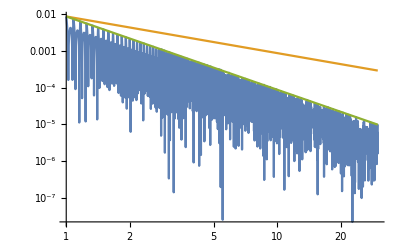

SequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

0.992173

```mathematica
LogLogPlot[{Abs[N[s[1/n]] - exactlimit[1,1]],0.00881251776213976/n,0.00881251776213976/n^2},{n,1,30}]
```

```mathematica
exactlimit[1,1]//N
```

1.04492

```mathematica
Abs[N[s[1]] - exactlimit[1,1]]
```

0.00881252

```mathematica
h^2/(1/n^(3/2))/.h-> 1/n
```

1/(√n)

```mathematica
f[i_,n_]:=PDF[NormalDistribution[Subscript[x,i],1/√n],Subscript[x,i+1]](1-Exp[-2 n (g - Subscript[x,i+1])(g - Subscript[x,i])])
```

```mathematica
i[n_]:=∏_(i=0)^(n-1) f[i,n]
```

```mathematica
i[6]
```

1/π^3 27 ⅇ^(-3 (-x_0+x_1)^2-3 (-x_1+x_2)^2-3 (-x_2+x_3)^2-3 (-x_3+x_4)^2-3 (-x_4+x_5)^2-3 (-x_5+x_6)^2) (1-ⅇ^(-12 (g-x_0) (g-x_1))) (1-ⅇ^(-12 (g-x_1) (g-x_2))) (1-ⅇ^(-12 (g-x_2) (g-x_3))) (1-ⅇ^(-12 (g-x_3) (g-x_4))) (1-ⅇ^(-12 (g-x_4) (g-x_5))) (1-ⅇ^(-12 (g-x_5) (g-x_6)))

```mathematica
Evaluate[D[i[1],{Subscript[x, 1]}]]/. Subscript[x, 1]-> 2/.g-> 2//Simplify
```

ⅇ^(-1/2 (-2+x_0)^2) √(2/π) (-2+x_0)

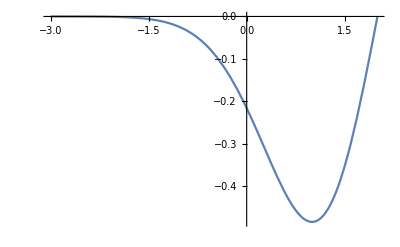

```mathematica
Plot[ⅇ^(-1/2 (-2+Subscript[x, 0])^2) √(2/π) (-2+Subscript[x, 0]),{Subscript[x, 0],-3,2}]
```

```mathematica
Evaluate[D[i[2],{Subscript[x, 2]}]]/. Subscript[x, 2]-> 2/.g-> 2//Simplify
```

(4 ⅇ^(-x_0^2-2 x_0 (-4+x_1)-2 (10-6 x_1+x_1^2)) (-1+ⅇ^(4 (-2+x_0) (-2+x_1))) (-2+x_1))/π

```mathematica
Plot3D[Evaluate[D[i[2],{Subscript[x, 2]}]]/. Subscript[x, 2]-> 2/.g-> 2,{Subscript[x, 0],-3,2},{Subscript[x, 1],-3,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
q[i_]:=PDF[NormalDistribution[Subscript[x,i],1/√n],Subscript[x,i+1]](1-Exp[-2 n (Subscript[g,i+1] - Subscript[x,i+1])(Subscript[g,i] - Subscript[x,i])])
```

```mathematica
u[i_]:=PDF[NormalDistribution[Subscript[x,i],1/√n],Subscript[x,i-1]](1-Exp[-2 n (Subscript[g,i-1] - Subscript[x,i-1])(Subscript[g,i] - Subscript[x,i])])
```

```mathematica
q[i]
```

(ⅇ^(-1/2 n (-x_i+x_(1+i))^2) (1-ⅇ^(-2 n (g_i-x_i) (g_(1+i)-x_(1+i)))) √n)/(√(2 π))

```mathematica
u[i]
```

(ⅇ^(-1/2 n (x_(-1+i)-x_i)^2) (1-ⅇ^(-2 n (g_(-1+i)-x_(-1+i)) (g_i-x_i))) √n)/(√(2 π))

```mathematica
Evaluate[D[u[i],{Subscript[x, i],1}]] /. Subscript[x, i]-> Subscript[g, i]
```

-ⅇ^(-1/2 n (-g_i+x_(-1+i))^2) n^(3/2) √(2/π) (g_(-1+i)-x_(-1+i))

```mathematica
Evaluate[D[u[i],{Subscript[x, i],1}]]Evaluate[D[q[i],{Subscript[x, i],2}]]/. Subscript[x, i]-> Subscript[g, i]
```

-(ⅇ^(-1/2 n (-g_i+x_(-1+i))^2) n^2 (g_(-1+i)-x_(-1+i)) (-4 ⅇ^(-1/2 n (-g_i+x_(1+i))^2) n^2 (g_(1+i)-x_(1+i))^2-4 ⅇ^(-1/2 n (-g_i+x_(1+i))^2) n^2 (g_(1+i)-x_(1+i)) (-g_i+x_(1+i))))/π

```mathematica
-(ⅇ^(-1/2 n (-Subscript[g, i]+Subscript[x, -1+i])^2) n^2 (Subscript[g, -1+i]-Subscript[x, -1+i]) (-4 ⅇ^(-1/2 n (-Subscript[g, i]+Subscript[x, 1+i])^2) n^2 (Subscript[g, 1+i]-Subscript[x, 1+i])^2-4 ⅇ^(-1/2 n (-Subscript[g, i]+Subscript[x, 1+i])^2) n^2 (Subscript[g, 1+i]-Subscript[x, 1+i]) (-Subscript[g, i]+Subscript[x, 1+i])))/π//FullSimplify
```

(4 ⅇ^(-1/2 n ((g_i-x_(-1+i))^2+(g_i-x_(1+i))^2)) n^4 (g_i-g_(1+i)) (-g_(-1+i)+x_(-1+i)) (g_(1+i)-x_(1+i)))/π

```mathematica
(4 ⅇ^(-1/2 n ((Subscript[g, i]-Subscript[x, -1+i])^2+(Subscript[g, i]-Subscript[x, 1+i])^2)) n^4 (Subscript[g, i]-Subscript[g, 1+i]) (-Subscript[g, -1+i]+Subscript[x, -1+i]) (Subscript[g, 1+i]-Subscript[x, 1+i]))/π//TeXForm
```

\frac{4 n^4 \left(g_i-g_{i+1}\right) \left(x_{i-1}-g_{i-1}\right) \left(g_{i+1}-x_{i+1}\right)
   \exp \left(-\frac{1}{2} n
   \left(\left(g_i-x_{i-1}\right){}^2+\left(g_i-x_{i+1}\right){}^2\right)\right)}{\pi }

```mathematica
Evaluate[D[u[i],{Subscript[x, i],1}]]Evaluate[D[q[i],{Subscript[x, i],2}]] +Evaluate[D[u[i],{Subscript[x, i],2}]]Evaluate[D[q[i],{Subscript[x, i],1}]]/. Subscript[x, i]-> Subscript[g, i] //FullSimplify
```

(4 ⅇ^(-1/2 n ((g_i-x_(-1+i))^2+(g_i-x_(1+i))^2)) n^4 (g_(-1+i)-2 g_i+g_(1+i)) (-g_(-1+i)+x_(-1+i)) (-g_(1+i)+x_(1+i)))/π

```mathematica
(4 ⅇ^(-1/2 n ((Subscript[g, i]-Subscript[x, -1+i])^2+(Subscript[g, i]-Subscript[x, 1+i])^2)) n^4 (Subscript[g, -1+i]-2 Subscript[g, i]+Subscript[g, 1+i]) (-Subscript[g, -1+i]+Subscript[x, -1+i]) (-Subscript[g, 1+i]+Subscript[x, 1+i]))/π//TeXForm
```

\frac{4 n^4 \left(g_{i-1}-2 g_i+g_{i+1}\right) \left(x_{i-1}-g_{i-1}\right)
   \left(x_{i+1}-g_{i+1}\right) \exp \left(-\frac{1}{2} n
   \left(\left(g_i-x_{i-1}\right){}^2+\left(g_i-x_{i+1}\right){}^2\right)\right)}{\pi }

```mathematica
∫_(-∞)^Subscript[g, i-1] (Subscript[g, i-1]-Subscript[x, i-1])PDF[NormalDistribution[0,1/(√n)],Subscript[x, i-1]-Subscript[g, i]]ⅆ Subscript[x, i-1]
```

ConditionalExpression[(ⅇ^(-1/2 n (g_(-1+i)-g_i)^2))/(√n √(2 π))+1/2 (1+Erf[(√n (g_(-1+i)-g_i))/(√2)]) (g_(-1+i)-g_i),(Re[n]≥0&&Re[n g_i]<0)||Re[n]>0]

```mathematica
∫_(-∞)^Subscript[g, i+1] (Subscript[g, i+1]-Subscript[x, i+1])PDF[NormalDistribution[0,1/(√n)],Subscript[x, i+1]-Subscript[g, i]]ⅆ Subscript[x, i+1]
```

ConditionalExpression[(ⅇ^(-1/2 n (g_i-g_(1+i))^2))/(√n √(2 π))+1/2 Erfc[(√n (g_i-g_(1+i)))/(√2)] (-g_i+g_(1+i)),(Re[n]≥0&&Re[n g_i]<0)||Re[n]>0]

```mathematica
(ⅇ^(-1/2 n (Subscript[g, i]-Subscript[g, 1+i])^2))/(√n √(2 π))+1/2 Erfc[(√n (Subscript[g, i]-Subscript[g, 1+i]))/(√2)] (-Subscript[g, i]+Subscript[g, 1+i])//TeXForm
```

\frac{1}{2} \left(g_{i+1}-g_i\right) \text{erfc}\left(\frac{\sqrt{n}
   \left(g_i-g_{i+1}\right)}{\sqrt{2}}\right)+\frac{e^{-\frac{1}{2} n
   \left(g_i-g_{i+1}\right){}^2}}{\sqrt{2 \pi } \sqrt{n}}

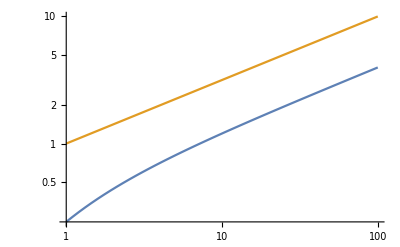

```mathematica
LogLogPlot[{PDF[NormalDistribution[0,1/(√n)],1/n],√n},{n,1,100}]
```

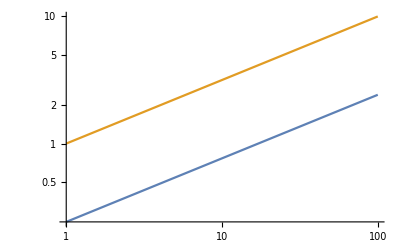

```mathematica
LogLogPlot[{PDF[NormalDistribution[0,1/(√n)],1/(√n)],√n},{n,1,100}]
```

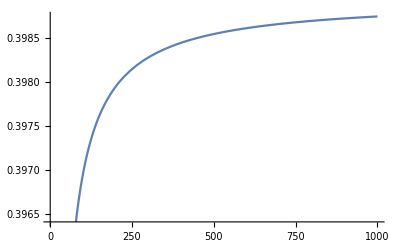

```mathematica
Plot[{PDF[NormalDistribution[0,1],1/(√n)]},{n,1,1000}]
```